```mathematica
(*Author of the Code : Maneesha Sushama Pradeep*)
```

# Factorial cumulants of proton multiplicities

## Preparations

```mathematica
a1Time=AbsoluteTime[]
```

3.982545081326247×10^9

```mathematica
SetDirectory["/Users/maneeshasushamapradeep/Documents/phd/5.Freezing_out_non-Gaussian_fluctuations/TablesWithFullCalculation/"] (*Directory where you saved the downloaded PDG files *)
```

/Users/maneeshasushamapradeep/Documents/phd/5.Freezing_out_non-Gaussian_fluctuations/TablesWithFullCalculation

```mathematica
PlotFolder="../DraftInPreparationSep/Plots/"
```

../DraftInPreparationSep/Plots/

### Mapping Parameters to be Input

```mathematica
Clear[α1,α2,μcMeV,ρ,w,TcGeV]
```

```mathematica
μcMeV=600;
α2=0Degree;
ρ=0.5;
w=5;
```

## Some Ising Calculations

```mathematica
a=-0.76201;
b=0.00804;
beta=0.326;
delta=4.8;
h0=0.36;
M0=0.605;
β=beta;
δ=delta;
βδ=beta delta;
htilde[θ_]:=h0(θ+a θ^3+b θ^5);
zmax:=3.;
wmax:=zmax^(-1/βδ);
θ1=θ/.FindRoot[htilde[θ],{θ,1.2}];
AcbyMuc4=100;
(* Create three interpolating functions: for r>0, r<0 and r small*)
Off[FindRoot::nlnum,ReplaceAll::reps] (* suppress some errors *)
θpz=FunctionInterpolation[θ/.FindRoot[z-htilde[θ](1-θ^2)^-βδ,{θ,0.9}],{z,0,zmax}];
θmz=FunctionInterpolation[θ/.FindRoot[z-htilde[θ](θ^2-1)^-βδ,{θ,1.1}],{z,0,zmax}];
θw=FunctionInterpolation[θ/.FindRoot[w-htilde[θ]^(-1/βδ)(1-θ^2),{θ,1.}],{w,-wmax,wmax}];
h[R_,θ_]=h0 R^(βδ)(θ+a θ^3+b θ^5);
r[R_,θ_]= R(1- θ^2);
c0=β (1+a+b)/(β+β δ);
α=2-β-(β δ);
c1=-(1/2) (α-1)^(-1)*((1-2β)(1+a+b)-2β (a+2 b));
c2=-(1/(2(α)))(2β b-(1-2β)(a+2b));
c3=-(1/(2(α+1)))b(1-2β);
g[θ_]=c0+c1(1-θ^2)+ c2 (1-θ^2)^2+c3 (1-θ^2)^3;
Pcrit[R_,θ_]=h0 M0 R^(β+β δ)(θ^2 ( (1+ a θ^2+ b θ^4))-g[θ]);
(* Define mapping functions *)
θrh[r_,h_]:=Module[{z,w},
z:= Abs[h r^-βδ]/;r≠0;
w:=r Abs[h]^(-1/βδ)/;h≠0;
Which[
h==0,If[r≥0,0,θ1],
r==0,Sign[h],
z≤zmax,Sign[h]If[r>0,θpz[z],θmz[z]],
z>zmax,Sign[h]θw[w]
]
]
Rrh[r_,h_]:=If[r==0,(Abs[h]/htilde[1])^(1/βδ),r(1-θrh[r,h]^2)^-1]
```

```mathematica
DRDr[R_,θ_]={dRdr}/.Solve[{D[r[R,θ],R]dRdr+D[r[R,θ],θ] dθdr==1,D[h[R,θ],R]dRdr+D[h[R,θ],θ] dθdr==0},{dRdr,dθdr}][[1]]//FullSimplify;
DθDr[R_,θ_]={dθdr}/.Solve[{D[r[R,θ],R]dRdr+D[r[R,θ],θ] dθdr==1,D[h[R,θ],R]dRdr+D[h[R,θ],θ] dθdr==0},{dRdr,dθdr}][[1]]//FullSimplify;
DRDh[R_,θ_]={dRdh}/.Solve[{D[r[R,θ],R]dRdh+D[r[R,θ],θ] dθdh==0,D[h[R,θ],R]dRdh+D[h[R,θ],θ] dθdh==1},{dRdh,dθdh}][[1]]//FullSimplify;
DθDh[R_,θ_]={dθdh}/.Solve[{D[r[R,θ],R]dRdh+D[r[R,θ],θ] dθdh==0,D[h[R,θ],R]dRdh+D[h[R,θ],θ] dθdh==1},{dRdh,dθdh}][[1]]//FullSimplify;
(*DRDr[R_,θ_]=D[htilde[θ],θ]/(2βδ θ htilde[θ]+(1-θ^2)D[htilde[θ],θ]);
DRDh[R_,θ_]=2θ R^(-βδ+1) (2βδ θ htilde[θ]+(1-θ^2)D[htilde[θ],θ])^(-1);
DθDr[R_,θ_]=-(βδ/R)htilde[θ]/(2βδ θ htilde[θ]+(1-θ^2)D[htilde[θ],θ]);
DθDh[R_,θ_]=(1-θ^2) R^-βδ (2βδ θ htilde[θ]+(1-θ^2)D[htilde[θ],θ])^(-1);*)
```

```mathematica
Ph[R_,θ_]=(DRDh[R,θ])D[Pcrit[R,θ],{R,1}]+DθDh[R,θ]D[Pcrit[R,θ],{θ,1}]//FullSimplify;
Pr[R_,θ_]=(DRDr[R,θ])D[Pcrit[R,θ],{R,1}]+DθDr[R,θ]D[Pcrit[R,θ],{θ,1}]//FullSimplify;
```

```mathematica
Phh[R_,θ_]=(DRDh[R,θ])D[Ph[R,θ],{R,1}]+DθDh[R,θ]D[Ph[R,θ],{θ,1}]//FullSimplify;
Phr[R_,θ_]=(DRDr[R,θ])D[Ph[R,θ],{R,1}]+DθDr[R,θ]D[Ph[R,θ],{θ,1}]//FullSimplify;
Prr[R_,θ_]=(DRDr[R,θ])D[Pr[R,θ],{R,1}]+DθDr[R,θ]D[Pr[R,θ],{θ,1}]//FullSimplify;
P2[R_,θ_]={Phh[R,θ][[1]],Phr[R,θ][[1]],Prr[R,θ][[1]]};
```

```mathematica
Phhh[R_,θ_]=(DRDh[R,θ])D[Phh[R,θ],{R,1}]+(DθDh[R,θ])D[Phh[R,θ],{θ,1}];
Prrh[R_,θ_]=(DRDh[R,θ])D[Prr[R,θ],{R,1}]+(DθDh[R,θ])D[Prr[R,θ],{θ,1}];
Phhr[R_,θ_]=(DRDr[R,θ])D[Phh[R,θ],{R,1}]+(DθDr[R,θ])D[Phh[R,θ],{θ,1}];
Prrr[R_,θ_]=(DRDr[R,θ])D[Prr[R,θ],{R,1}]+(DθDr[R,θ])D[Prr[R,θ],{θ,1}];
P3[R_,θ_]={Phhh[R,θ][[1]],Phhr[R,θ][[1]],Prrh[R,θ][[1]],Prrr[R,θ][[1]]};
```

```mathematica
Phhhh[R_,θ_]=(DRDh[R,θ])D[Phhh[R,θ],{R,1}]+(DθDh[R,θ])D[Phhh[R,θ],{θ,1}];
Prrhh[R_,θ_]=(DRDh[R,θ])D[Prrh[R,θ],{R,1}]+(DθDh[R,θ])D[Prrh[R,θ],{θ,1}];
Phhhr[R_,θ_]=(DRDr[R,θ])D[Phhh[R,θ],{R,1}]+(DθDr[R,θ])D[Phhh[R,θ],{θ,1}];
Prrrh[R_,θ_]=(DRDr[R,θ])D[Prrh[R,θ],{R,1}]+(DθDr[R,θ])D[Prrh[R,θ],{θ,1}];
Prrrr[R_,θ_]=(DRDr[R,θ])D[Prrr[R,θ],{R,1}]+(DθDr[R,θ])D[Prrr[R,θ],{θ,1}];
P4[R_,θ_]={Phhhh[R,θ][[1]],Phhhr[R,θ][[1]],Prrhh[R,θ][[1]],Prrrh[R,θ][[1]],Prrrr[R,θ][[1]]};
```

```mathematica
(*P is essentially Psing/Tc^4*)
```

## Phase boundary from lattice

#### Slope, Tc formulas

```mathematica
KappaParameterInLatticeParametrizationOfPhaseBoundary=-0.0153;
T0=158;
A1=0.035;
A2=1.47;
a2=0.652;
a3=-2.60;
b0=21.4;
b1=-9.81;

κ2BB[T_]=(A1*b0*(T/0.200)+a2*(T/0.200)^2+a3*(T/0.200)^3+A2*(T/0.200)^4)/(b0+b1*(T/0.200)+(T/0.200)^2);
Dκ2BBT[T_]=D[κ2BB[T],T];

Tcritical[u_]:=Select[(T/.NSolve[T(1+κ2BB[T]((u)/T)^2)==(T0*0.001),T,Reals]),Positive][[1]];
TcriticalTable=Table[{u,Tcritical[u]},{u,0,0.95,0.01}];
TcriticalInt=Interpolation[TcriticalTable];
DTcritDT[u_]:=Tcritical[u](Dκ2BBT[Tcritical[u]]*(u/Tcritical[u])^2-2(u^2/Tcritical[u]^3)κ2BB[Tcritical[u]])+1+κ2BB[Tcritical[u]](u/Tcritical[u])^2;
Alpha1[u_]:=ArcTan[2κ2BB[Tcritical[u]]*(u/Tcritical[u])*(1/DTcritDT[u])];
```

```mathematica
Alpha1[0.6]
```

0.289971

#### Mapping Parameters

```mathematica
TcParotto[u_]=(T0+(KappaParameterInLatticeParametrizationOfPhaseBoundary/T0)(u*1000)^2)*0.001;(*used by Parotto et Al*)
α1=(*-(ArcTan[2(KappaParameterInLatticeParametrizationOfPhaseBoundary/T0)μcMeV])*)Alpha1[μcMeV*0.001](**used by Parotto et Al*);

μcGeV=μcMeV*0.001;
TcGeV=(*TcMeV*0.001;*)TcriticalInt[μcGeV] (*0.097*);
TcMeV=TcGeV*0.001;
(*α1=Alpha1[μcMeV*0.001];*)


A=TcMeV^4;

hu=-Sin[α1]/(w TcGeV Sin[α1-α2]);
hT=-Cos[α1]/(w TcGeV Sin[α1-α2]);
ru=Sin[α2]/(ρ w TcGeV Sin[α1-α2]);
rT=Cos[α2]/(ρ w TcGeV Sin[α1-α2]);
(*rfxn[u_,T_]=ru (u-μcGeV)+rT(T-TcGeV);
hfxn[u_,T_]=hu (u-μcGeV)+hT(T-TcGeV);(*linear*)*)
α12prime=ArcTan[Tan[α1]-Tan[α2]];
α12prime/Degree;
s12prime=Sign[Sin[α1-α2]/Cos[α1]]Abs[(Tan[α1]-Tan[α2])/Sqrt[1+(Tan[α1]-Tan[α2])^2]];
c12prime=If[Cos[α2]>=0,Sqrt[1-(s12prime)^2],-Sqrt[1-(s12prime)^2]];
wprime=(w/Cos[α1])*Sqrt[(Cos[α1]Cos[α2])^2+(Sin[α1-α2])^2];
ρprime=ρ*(Cos[α1])^2/(Sqrt[(Cos[α1]Cos[α2])^2+(Sin[α1-α2])^2]);
hfxn[u_,T_]=-(T(1+κ2BB[T]((u)/T)^2)-(T0*0.001))/(wprime*TcGeV*DTcritDT[μcGeV]*s12prime);
rfxn[u_,T_]=-((1/(2*μcGeV *TcGeV*wprime*ρprime)) (u^2-μcGeV^2))-(1/ρprime)hfxn[u,T]*c12prime;
```

#### Freeze-out curve : TμFGen[u,DelT] is such that T_c(μ_c)-Tf=DelT (in GeV)

```mathematica
TCF=158;
a1=1307.5;
TF[sqrts_]=TCF/(1+Exp[2.60−(Log[(sqrts)]/0.45)]);
μF[sqrts_]=a1/(1+0.288 sqrts);
CrossOverLine[u_]:=TcriticalInt[u];
TμFGen[u_,DelT_]=TcriticalInt[u]-DelT;
SQRTS[u_]=((a1/(u*1000))-1)(0.288)^(-1);
```

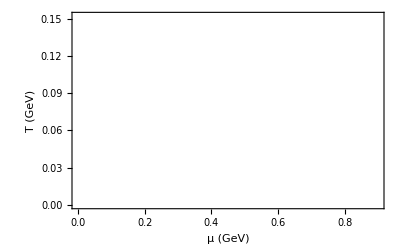

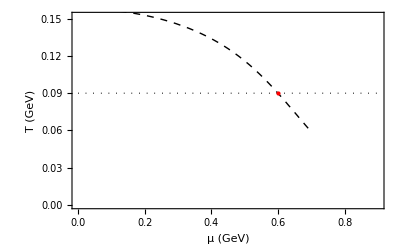

```mathematica
DelT1=0.004;
DelT2=0.006;
DelT3=0.009;
TFPlot=Plot[{TμFGen[u,DelT2]},{u,0.0,0.9},Frame->True,FrameLabel->{"μ (GeV)","T (GeV)"}, LabelStyle->{18,Bold,Black},PlotStyle->{White}]
HPlot=ContourPlot[hfxn[u,T],{u,0.0,0.9},{T,0.06,0.2},Contours->{0},ContourShading->None,ContourStyle->{White,Dashed},PlotRange->All];
RPlot=ContourPlot[rfxn[u,T],{u,0.0,0.9},{T,0.06,0.2},Contours->{0},ContourShading->None,ContourStyle->{White,Dotted},PlotRange->All];
Show[TFPlot,HPlot,RPlot,Graphics[{Red,PointSize@Large,Point[{(μcGeV),TcriticalInt[μcGeV]}]}]]

Clear[DelT1];
```

## Non-critical correlations in Hadron Resonance Gas due to Statistics

### PDG List From SMASHPlus 20126

```mathematica
(*The particles included in the calculation are from PDG2016PlusList contains information from PDGList used in SMASH - can be obtained from https://github.com/jordissm/PDG2021Plus/tree/main/hadron-lists/PDG2016Plus/for_Thermal-FIST*)
(*sortedHadronProperties contain Name of Hadron, mass of Particle in GeV, Degenracy, Baryon Charge, Whether particle is Fermion/Boson (1,-1), particle ID No*)
```

```mathematica
PDG2021PlusList=Import["PDG2021Plus_ThFIST_JMK_anti.dat","Table"];
```

```mathematica
len=Length[PDG2021PlusList];
sortedHadronProperties=SortBy[Table[{PDG2021PlusList[[i,2]],PDG2021PlusList[[i,4]],PDG2021PlusList[[i,5]],PDG2021PlusList[[i,7]],PDG2021PlusList[[i,6]],PDG2021PlusList[[i,1]]},{i,1,Length[PDG2021PlusList]}],#[[2]]&];
sortedHadronProperties=Delete[sortedHadronProperties,1];
```

### Resonance Decays

```mathematica
(*Load and clean file*)lines=Import["decays_PDG2021Plus_ThFIST.dat","Lines"];
cleaned=StringTrim/@Select[lines,StringMatchQ[#,Except["#"]~~___]&];
blocks=SplitBy[cleaned,#=!=""&];
blocks=Select[blocks,#[[1]]=!=""&];

(*Proton PDG ID*)
protonIDR=2212;

(*Step 1:Parse into association*)
decayRules=Association@Table[Module[{pdg,n,channels,parsedChannels},pdg=ToExpression[block[[1]]];
n=ToExpression[block[[2]]];
channels=block[[3;;2+n]];
parsedChannels=Table[Module[{parts=StringSplit[ch]},{ToExpression[parts[[1]]],ToExpression/@parts[[2;;]]}],{ch,channels}];
pdg->parsedChannels],{block,blocks}];

(*Step 2:Recursively compute total probability of ending in a proton*)
ClearAll[ProtonProb]
ProtonProb[pid_]:=(*ProtonProb[pid]=*)Module[{channels,prob=0},If[pid===protonIDR,Return[1.]];
If[!KeyExistsQ[decayRules,pid],Return[0.]];(*stable or unknown*)channels=decayRules[pid];
Do[Module[{br,daughters,daughterProbs},{br,daughters}=ch;
daughterProbs=1-Times@@(1-ProtonProb[#]&/@daughters);(*probability that at least one daughter leads to proton*)prob+=br*daughterProbs;],{ch,channels}];
prob];

(*Example:compute for all particles in the decay table*)
result=Table[{pid,ProtonProb[pid]},{pid,Keys[decayRules]}];

(*Sort descending by probability*)
ProbabilityToDecayToProton=Select[SortBy[result,-#[[2]]&],#[[2]]=!=0.&];
IDConversionTable=Table[{i,Flatten[Position[sortedHadronProperties[[All,6]],ProbabilityToDecayToProton[[i,1]]]][[1]]},{i,1,Length[ProbabilityToDecayToProton]}];
(*IDConversionTable=Delete[IDConversionTable,76];*)
IDConversionTable[[76,2]]=Flatten[Position[sortedHadronProperties[[All,6]],1130]][[1]];
```

Part::partw: Part 1 of {} does not exist.

### Kinetic Functions related to Non-critical correlations in the gas

```mathematica
Hvec[u_,T_,i_]:={(Sqrt[sortedHadronProperties[[i,2]]^2+p^2]/T),sortedHadronProperties[[i,4]]}
```

```mathematica
fA[i_,p_,u_,T_]:=(Exp[Sqrt[(sortedHadronProperties[[i,2]])^2+p^2]/T]Exp[-sortedHadronProperties[[i,4]](u/T)] +sortedHadronProperties[[i,5]])^(-1)
fAprime[i_,p_,u_,T_]:=fA[i,p, u,T]*(1-(sortedHadronProperties[[i,5]]fA[i,p, u,T]))
```

```mathematica
Gi2[i_,p_,u_,T_]:=fAprime[i,p,u,T]
```

```mathematica
Gi3[i_,p_,u_,T_]:=fA[i,p, u,T]*(1-(sortedHadronProperties[[i,5]]fA[i,p, u,T]))*(1-(2sortedHadronProperties[[i,5]]fA[i,p, u,T]))
```

```mathematica
Gi4[i_,p_,u_,T_]:=fA[i,p, u,T]*(1-(sortedHadronProperties[[i,5]]fA[i,p, u,T]))*(1-(6sortedHadronProperties[[i,5]]fA[i,p, u,T])(1-(sortedHadronProperties[[i,5]]*fA[i,p, u,T])))
```

```mathematica
Hϵn2[u_,T_]:=(2π^2)^(-1)T^(-3)NIntegrate[Sum[sortedHadronProperties[[i,3]]*Gi2[i,p,u,T]p^2(Outer[Times,Hvec[u,T,i],Hvec[u,T,i]]),{i,1,Length[sortedHadronProperties]}],{p,0,∞}]
```

```mathematica
Hϵn2Inverse[u_,T_]:=Inverse[Hϵn2[u,T]]
```

```mathematica
Hϵn3[u_,T_]:=(2π^2)^(-1)T^(-3)NIntegrate[Sum[sortedHadronProperties[[i,3]]*Gi3[i,p,u,T]p^2(Outer[Times,Hvec[u,T,i],Hvec[u,T,i],Hvec[u,T,i]]),{i,1,Length[sortedHadronProperties]}],{p,0,∞}]
```

```mathematica
Hϵn4[u_,T_]:=(2π^2)^(-1)T^(-3)NIntegrate[Sum[sortedHadronProperties[[i,3]]*Gi4[i,p,u,T]p^2(Outer[Times,Hvec[u,T,i],Hvec[u,T,i],Hvec[u,T,i],Hvec[u,T,i]]),{i,1,Length[sortedHadronProperties]}],{p,0,∞}]
```

```mathematica
protonID=18;
KinCoef[u_,T_]:=(2π^2)^(-1)T^(-3)sortedHadronProperties[[protonID,3]]Dot[Hϵn2Inverse[u,T],NIntegrate[Gi2[protonID,p,u,T]p^2*Hvec[u,T,protonID],{p,0,∞}]];
```

```mathematica
Hϵn2InverseATCP=Hϵn2Inverse[μcGeV,TcGeV];
Hϵn3ATCP=Hϵn3[μcGeV,TcGeV];
Hϵn4ATCP=Hϵn4[μcGeV,TcGeV];
```

## Hydrodynamic Ising like Correlation functions - Equations And Plots

### Equations

```mathematica
(*All hydrodynamic correlation functions below are made dimensionless by dividing by appropriate factors of Tc and taking derivatives of P/Tc^4 instead of P. There are hidden factors of V which actually give dimension, but they get divided by again hidden factors of V in the integrations*)
```

```mathematica
Hbb[u_,T_]:=(hu*TcGeV)^2 Phh[Rrh[rfxn[u,T],hfxn[u,T]],θrh[rfxn[u,T],hfxn[u,T]]]+2(hu*TcGeV)(ru*TcGeV) Phr[Rrh[rfxn[u,T],hfxn[u,T]],θrh[rfxn[u,T],hfxn[u,T]]]+
(ru*TcGeV)^2Prr[Rrh[rfxn[u,T],hfxn[u,T]],θrh[rfxn[u,T],hfxn[u,T]]]
Hen[u_,T_]:=(μcGeV/TcGeV)^(1)((ru*TcGeV)^2Prr[Rrh[rfxn[u,T],hfxn[u,T]],θrh[rfxn[u,T],hfxn[u,T]]]+(hu*TcGeV)^2Phh[Rrh[rfxn[u,T],hfxn[u,T]],θrh[rfxn[u,T],hfxn[u,T]]]+2(hu*ru*TcGeV^2)Phr[Rrh[rfxn[u,T],hfxn[u,T]],θrh[rfxn[u,T],hfxn[u,T]]])+(((ru*TcGeV)(rT*TcGeV))Prr[Rrh[rfxn[u,T],hfxn[u,T]],θrh[rfxn[u,T],hfxn[u,T]]]+((hu*TcGeV)(hT*TcGeV))Phh[Rrh[rfxn[u,T],hfxn[u,T]],θrh[rfxn[u,T],hfxn[u,T]]]+((hu*rT*TcGeV^2)+(hT*ru*TcGeV^2))Phr[Rrh[rfxn[u,T],hfxn[u,T]],θrh[rfxn[u,T],hfxn[u,T]]])
Hee[u_,T_]:=(μcGeV/TcGeV)^(2)((ru*TcGeV)^2Prr[Rrh[rfxn[u,T],hfxn[u,T]],θrh[rfxn[u,T],hfxn[u,T]]]+(hu*TcGeV)^2Phh[Rrh[rfxn[u,T],hfxn[u,T]],θrh[rfxn[u,T],hfxn[u,T]]]+2(hu*ru*TcGeV^2)Phr[Rrh[rfxn[u,T],hfxn[u,T]],θrh[rfxn[u,T],hfxn[u,T]]])+2*(μcGeV/TcGeV)^(1)(((ru*TcGeV)(rT*TcGeV))Prr[Rrh[rfxn[u,T],hfxn[u,T]],θrh[rfxn[u,T],hfxn[u,T]]]+((hu*TcGeV)(hT*TcGeV))Phh[Rrh[rfxn[u,T],hfxn[u,T]],θrh[rfxn[u,T],hfxn[u,T]]]+((hu*rT*TcGeV^2)+(hT*ru*TcGeV^2))Phr[Rrh[rfxn[u,T],hfxn[u,T]],θrh[rfxn[u,T],hfxn[u,T]]])+((rT*TcGeV)^2Prr[Rrh[rfxn[u,T],hfxn[u,T]],θrh[rfxn[u,T],hfxn[u,T]]]+(hT*TcGeV)^2Phh[Rrh[rfxn[u,T],hfxn[u,T]],θrh[rfxn[u,T],hfxn[u,T]]]+2(hT*rT*TcGeV^2)Phr[Rrh[rfxn[u,T],hfxn[u,T]],θrh[rfxn[u,T],hfxn[u,T]]])
ΔH2ϵn[u_,T_]:={{Hee[u,T][[1]],Hen[u,T][[1]]},{Hen[u,T][[1]],Hbb[u,T][[1]]}}
```

```mathematica
Hbb3[u_,T_]:=(hu*TcGeV)^3 Phhh[Rrh[rfxn[u,T],hfxn[u,T]],θrh[rfxn[u,T],hfxn[u,T]]]+3(hu*TcGeV)^2(ru*TcGeV) Phhr[Rrh[rfxn[u,T],hfxn[u,T]],θrh[rfxn[u,T],hfxn[u,T]]]+
3(ru*TcGeV)^2(hu*TcGeV) Prrh[Rrh[rfxn[u,T],hfxn[u,T]],θrh[rfxn[u,T],hfxn[u,T]]]+(ru*TcGeV)^3 Prrr[Rrh[rfxn[u,T],hfxn[u,T]],θrh[rfxn[u,T],hfxn[u,T]]]
Hss3[u_,T_]:=(hT*TcGeV)^3 Phhh[Rrh[rfxn[u,T],hfxn[u,T]],θrh[rfxn[u,T],hfxn[u,T]]]+3(hT*TcGeV)^2(rT*TcGeV) Phhr[Rrh[rfxn[u,T],hfxn[u,T]],θrh[rfxn[u,T],hfxn[u,T]]]+
3(rT*TcGeV)^2(hT*TcGeV) Prrh[Rrh[rfxn[u,T],hfxn[u,T]],θrh[rfxn[u,T],hfxn[u,T]]]+(rT*TcGeV)^3 Prrr[Rrh[rfxn[u,T],hfxn[u,T]],θrh[rfxn[u,T],hfxn[u,T]]]
Hs1n2[u_,T_]:=(hu*TcGeV)^2(hT*TcGeV) Phhh[Rrh[rfxn[u,T],hfxn[u,T]],θrh[rfxn[u,T],hfxn[u,T]]]+((hu*TcGeV)^2(rT*TcGeV)+2(hu*TcGeV)(hT*TcGeV)(ru*TcGeV)) Phhr[Rrh[rfxn[u,T],hfxn[u,T]],θrh[rfxn[u,T],hfxn[u,T]]]+
((ru*TcGeV)^2(hT*TcGeV)+2(ru*TcGeV)(rT*TcGeV)(hu*TcGeV))Prrh[Rrh[rfxn[u,T],hfxn[u,T]],θrh[rfxn[u,T],hfxn[u,T]]]+(ru*TcGeV)^2(rT*TcGeV) Prrr[Rrh[rfxn[u,T],hfxn[u,T]],θrh[rfxn[u,T],hfxn[u,T]]]
Hs2n1[u_,T_]:=(hT*TcGeV)^2(hu*TcGeV) Phhh[Rrh[rfxn[u,T],hfxn[u,T]],θrh[rfxn[u,T],hfxn[u,T]]]+((hT*TcGeV)^2(ru*TcGeV)+2(hu*TcGeV)(rT*TcGeV)(hT*TcGeV)) Phhr[Rrh[rfxn[u,T],hfxn[u,T]],θrh[rfxn[u,T],hfxn[u,T]]]+
((rT*TcGeV)^2(hu*TcGeV)+2(rT*TcGeV)(ru*TcGeV)(hT*TcGeV))Prrh[Rrh[rfxn[u,T],hfxn[u,T]],θrh[rfxn[u,T],hfxn[u,T]]]+(ru*TcGeV)(rT*TcGeV)^2 Prrr[Rrh[rfxn[u,T],hfxn[u,T]],θrh[rfxn[u,T],hfxn[u,T]]]
Hee3[u_,T_]:=(μcGeV/TcGeV)^3 Hbb3[u,T]+3(μcGeV/TcGeV)^2 Hs1n2[u,T]+3(μcGeV/TcGeV) Hs2n1[u,T]+ Hss3[u,T]
He2n1[u_,T_]:=(μcGeV/TcGeV)^2 Hbb3[u,T]+2(μcGeV/TcGeV) Hs1n2[u,T]+Hs2n1[u,T]
He1n2[u_,T_]:=(μcGeV/TcGeV) Hbb3[u,T]+ Hs1n2[u,T]
ΔH3ϵn[u_,T_]:={{{Hee3[u,T][[1]],He2n1[u,T][[1]]},{He2n1[u,T][[1]],He1n2[u,T][[1]]}},{{He2n1[u,T][[1]],He1n2[u,T][[1]]},{He1n2[u,T][[1]],Hbb3[u,T][[1]]}}}
```

```mathematica
Hbb4[u_,T_]:=(hu*TcGeV)^4 Phhhh[Rrh[rfxn[u,T],hfxn[u,T]],θrh[rfxn[u,T],hfxn[u,T]]]+4(hu*TcGeV)^3(ru*TcGeV) Phhhr[Rrh[rfxn[u,T],hfxn[u,T]],θrh[rfxn[u,T],hfxn[u,T]]]+
4(ru*TcGeV)^3(hu*TcGeV) Prrrh[Rrh[rfxn[u,T],hfxn[u,T]],θrh[rfxn[u,T],hfxn[u,T]]]+6(hu*TcGeV)^2(ru*TcGeV)^2 Prrhh[Rrh[rfxn[u,T],hfxn[u,T]],θrh[rfxn[u,T],hfxn[u,T]]]+(ru*TcGeV)^4 Prrrr[Rrh[rfxn[u,T],hfxn[u,T]],θrh[rfxn[u,T],hfxn[u,T]]]
Hss4[u_,T_]:=(hT*TcGeV)^4 Phhhh[Rrh[rfxn[u,T],hfxn[u,T]],θrh[rfxn[u,T],hfxn[u,T]]]+4(hT*TcGeV)^3(rT*TcGeV) Phhhr[Rrh[rfxn[u,T],hfxn[u,T]],θrh[rfxn[u,T],hfxn[u,T]]]+
4(rT*TcGeV)^3(hT*TcGeV) Prrrh[Rrh[rfxn[u,T],hfxn[u,T]],θrh[rfxn[u,T],hfxn[u,T]]]+6(hT*TcGeV)^2(rT*TcGeV)^2 Prrhh[Rrh[rfxn[u,T],hfxn[u,T]],θrh[rfxn[u,T],hfxn[u,T]]]+(rT*TcGeV)^4 Prrrr[Rrh[rfxn[u,T],hfxn[u,T]],θrh[rfxn[u,T],hfxn[u,T]]]
Hs3n1[u_,T_]:=(hT*TcGeV)^3(hu*TcGeV) Phhhh[Rrh[rfxn[u,T],hfxn[u,T]],θrh[rfxn[u,T],hfxn[u,T]]]+((hT*TcGeV)^3(ru*TcGeV)+3 (hT*TcGeV)^2(hu*TcGeV)(rT*TcGeV))Phhhr[Rrh[rfxn[u,T],hfxn[u,T]],θrh[rfxn[u,T],hfxn[u,T]]]+
((rT*TcGeV)^3(hu*TcGeV)+3 (rT*TcGeV)^2(ru*TcGeV)(hT*TcGeV)) Prrrh[Rrh[rfxn[u,T],hfxn[u,T]],θrh[rfxn[u,T],hfxn[u,T]]]+(3(hT*TcGeV)(hu*TcGeV)(rT*TcGeV)^2+3(hT*TcGeV)^2(ru*TcGeV)(rT*TcGeV)) Prrhh[Rrh[rfxn[u,T],hfxn[u,T]],θrh[rfxn[u,T],hfxn[u,T]]]+(ru*TcGeV)(rT*TcGeV)^3 Prrrr[Rrh[rfxn[u,T],hfxn[u,T]],θrh[rfxn[u,T],hfxn[u,T]]]
Hs1n3[u_,T_]:=(hT*TcGeV)(hu*TcGeV)^3 Phhhh[Rrh[rfxn[u,T],hfxn[u,T]],θrh[rfxn[u,T],hfxn[u,T]]]+((hu*TcGeV)^3(rT*TcGeV)+3 (hu*TcGeV)^2(hT*TcGeV)(ru*TcGeV))Phhhr[Rrh[rfxn[u,T],hfxn[u,T]],θrh[rfxn[u,T],hfxn[u,T]]]+
((ru*TcGeV)^3(hT*TcGeV)+3 (ru*TcGeV)^2(rT*TcGeV)(hu*TcGeV)) Prrrh[Rrh[rfxn[u,T],hfxn[u,T]],θrh[rfxn[u,T],hfxn[u,T]]]+(3(hu*TcGeV)(hT*TcGeV)(ru*TcGeV)^2+3(hu*TcGeV)^2(rT*TcGeV)(ru*TcGeV)) Prrhh[Rrh[rfxn[u,T],hfxn[u,T]],θrh[rfxn[u,T],hfxn[u,T]]]+(rT*TcGeV)(ru*TcGeV)^3 Prrrr[Rrh[rfxn[u,T],hfxn[u,T]],θrh[rfxn[u,T],hfxn[u,T]]]
Hs2n2[u_,T_]:=(hT*TcGeV)^2(hu*TcGeV)^2Phhhh[Rrh[rfxn[u,T],hfxn[u,T]],θrh[rfxn[u,T],hfxn[u,T]]]+(2 (hu*TcGeV)(ru*TcGeV)(hT*TcGeV)^2+2 (hu*TcGeV)^2(hT*TcGeV)(rT*TcGeV))Phhhr[Rrh[rfxn[u,T],hfxn[u,T]],θrh[rfxn[u,T],hfxn[u,T]]]+
(2(ru*TcGeV)^2(rT*TcGeV)(hT*TcGeV)+2(rT*TcGeV)^2(ru*TcGeV)(hu*TcGeV)) Prrrh[Rrh[rfxn[u,T],hfxn[u,T]],θrh[rfxn[u,T],hfxn[u,T]]]+((hT*TcGeV)(hT*TcGeV)(ru*TcGeV)^2+(hu*TcGeV)^2(rT*TcGeV)(rT*TcGeV)+4(hu*TcGeV)(ru*TcGeV)(hT*TcGeV)(rT*TcGeV)) Prrhh[Rrh[rfxn[u,T],hfxn[u,T]],θrh[rfxn[u,T],hfxn[u,T]]]+(rT*TcGeV)^2(ru*TcGeV)^2 Prrrr[Rrh[rfxn[u,T],hfxn[u,T]],θrh[rfxn[u,T],hfxn[u,T]]]
Hee4[u_,T_]:=(μcGeV/TcGeV)^4 Hbb4[u,T]+4(μcGeV/TcGeV)^3 Hs1n3[u,T]+4(μcGeV/TcGeV) Hs3n1[u,T]+ Hss4[u,T]+6(μcGeV/TcGeV)^2Hs2n2[u,T]
He3n1[u_,T_]:=(μcGeV/TcGeV)^3 Hbb4[u,T]+3(μcGeV/TcGeV)^2 Hs1n3[u,T]+ Hs3n1[u,T]+3(μcGeV/TcGeV)Hs2n2[u,T]
He2n2[u_,T_]:=(μcGeV/TcGeV)^2 Hbb4[u,T]+2(μcGeV/TcGeV) Hs1n3[u,T]+ Hs2n2[u,T]
He1n3[u_,T_]:=(μcGeV/TcGeV) Hbb4[u,T]+ Hs1n3[u,T]
ΔH4ϵn[u_,T_]:={{{{Hee4[u,T][[1]],He3n1[u,T][[1]]},{He3n1[u,T][[1]],He2n2[u,T][[1]]}},{{He3n1[u,T][[1]],He2n2[u,T][[1]]},{He2n2[u,T][[1]],He1n3[u,T][[1]]}}},{{{He3n1[u,T][[1]],He2n2[u,T][[1]]},{He2n2[u,T][[1]],He1n3[u,T][[1]]}},{{He2n2[u,T][[1]],He1n3[u,T][[1]]},{He1n3[u,T][[1]],Hbb4[u,T][[1]]}}}}
```

```mathematica
(*{0.2,0.3,0.4,0.5,0.6,0.7,0.8}, {1.8,2.2,2.6,3.0,3.4,3.8,5.0},{12,15,20,30.0,40,50}*)
```

### Plots

#### Two-point correlations

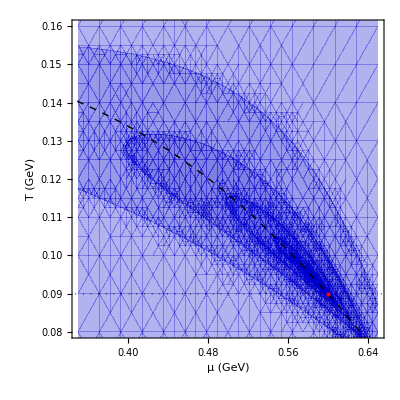

```mathematica
Hnn2=Show[ContourPlot[Hbb[u,T],{u,0.35,0.65},{T,0.06,0.2},PlotRange-> All,ContourShading->Flatten[{Table[RGBColor[0,0,0.8,i],{i,0.2,1.2,.1}]}],Contours->{0.01,0.05,0.1,0.2,0.1,0.2,0.4,0.6,0.8,1.0},ContourLabels-> None,ContourStyle->None,FrameStyle->{Black,Bold},LabelStyle->{18,Bold,Black},FrameLabel->{"μ (GeV)", "T (GeV)"}, LabelStyle->{18,Black,Bold}(*,PlotLegends->Automatic*)],HPlot,RPlot,Graphics[{Red,PointSize@Large,Point[{μcGeV,TcGeV}]}],PlotRange->{{0.35,0.65},{0.08,0.16}}]
```

```mathematica
Hbb3[0.6,0.1]
```

{-0.249045}

#### Three-point correlations

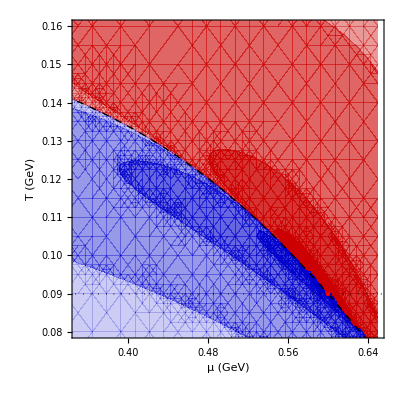

```mathematica
Hnn3Plot=Show[ContourPlot[Hbb3[u,T],{u,0.25,0.65},{T,0.06,0.2},PlotRange-> All,ContourShading->Flatten[{Table[RGBColor[0.8,0,0,i],{i,1.2,0.4,-.2}],Table[RGBColor[0,0,0.8,i],{i,0.2,1.0,.2}]}],Contours-> {-10,-1,-0.1,-0.01,0,0.01,0.1,1,10},ContourStyle->None,FrameStyle->{Black,Bold},LabelStyle->{18,Bold,Black},LabelStyle->{18,Bold,Black},FrameLabel->{"μ (GeV)", "T (GeV)"}(*,PlotLegends->Automatic*)],HPlot,RPlot,Graphics[{Red,PointSize@Large,Point[{μcGeV,TcGeV}]}],Graphics[{Red,PointSize@Large,Point[{μcGeV,TcGeV}]}],PlotRange->{{0.35,0.65},{0.08,0.16}}]
```

#### Four-point correlations

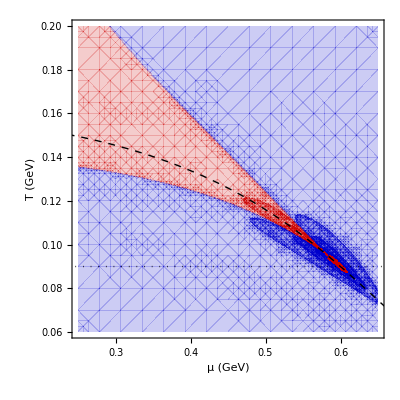

```mathematica
Hbb4Plot=Show[ContourPlot[Hbb4[u,T],{u,0.25,0.65},{T,0.06,0.2},PlotRange-> All,ContourShading->Flatten[{Table[RGBColor[0.8,0,0,i],{i,1.2,0.2,-.2}],Table[RGBColor[0,0,0.8,i],{i,0.2,1.0,.2}]}],Contours-> {-1000,-500,-100,-10,-1,0,1,10,100,500,1000},ContourStyle->None,FrameStyle->{Black,Bold},LabelStyle->{18,Bold,Black},FrameLabel->{"μ (GeV)", "T (GeV)"}(*,PlotLegends->Automatic*)],Graphics[{Red,PointSize@Large,Point[{μcGeV,TcGeV}]}],HPlot,RPlot,PlotRange->{{0.25,0.65},{0.06,0.2}},AspectRatio->1]
```

## Hydrodynamic IRCs

#### IRCS

```mathematica
IRCΔH3ϵn[u_,T_,i1_,i2_,i3_]:=ΔH3ϵn[u,T][[i1,i2,i3]]-Sum[ΔH2ϵn[u,T][[i1,j]]*Hϵn2InverseATCP[[j,k]]*Hϵn3ATCP[[k,i2,i3]],{j,1,2},{k,1,2}]-Sum[ΔH2ϵn[u,T][[i2,j]]*Hϵn2InverseATCP[[j,k]]*Hϵn3ATCP[[k,i3,i1]],{j,1,2},{k,1,2}]-Sum[ΔH2ϵn[u,T][[i3,j]]*Hϵn2InverseATCP[[j,k]]*Hϵn3ATCP[[k,i1,i2]],{j,1,2},{k,1,2}]
```

```mathematica
IRCΔH4ϵn[u_,T_,i1_,i2_,i3_,i4_]:=ΔH4ϵn[u,T][[i1,i2,i3,i4]]-Sum[(ΔH3ϵn[u,T][[i1,i2,j]]Hϵn2InverseATCP[[j,k]]Hϵn3ATCP[[k,i3,i4]]+ΔH3ϵn[u,T][[i2,i3,j]]Hϵn2InverseATCP[[j,k]]Hϵn3ATCP[[k,i1,i4]]+ΔH3ϵn[u,T][[i1,i4,j]]Hϵn2InverseATCP[[j,k]]Hϵn3ATCP[[k,i2,i3]]+ΔH3ϵn[u,T][[i1,i3,j]]Hϵn2InverseATCP[[j,k]]Hϵn3ATCP[[k,i2,i4]]+ΔH3ϵn[u,T][[i2,i4,j]]Hϵn2InverseATCP[[j,k]]Hϵn3ATCP[[k,i1,i3]]+ΔH3ϵn[u,T][[i3,i4,j]]Hϵn2InverseATCP[[j,k]]Hϵn3ATCP[[k,i1,i2]]),{j,1,2},{k,1,2}]-(Sum[ΔH2ϵn[u,T][[i1,j]]Hϵn2InverseATCP[[j,k]]Hϵn4ATCP[[k,i2,i3,i4]],{j,1,2},{k,1,2}]+Sum[ΔH2ϵn[u,T][[i2,j]]Hϵn2InverseATCP[[j,k]]Hϵn4ATCP[[k,i3,i4,i1]],{j,1,2},{k,1,2}]+Sum[ΔH2ϵn[u,T][[i3,j]]Hϵn2InverseATCP[[j,k]]Hϵn4ATCP[[k,i4,i1,i2]],{j,1,2},{k,1,2}]+Sum[ΔH2ϵn[u,T][[i4,j]]Hϵn2InverseATCP[[j,k]]Hϵn4ATCP[[k,i1,i2,i3]],{j,1,2},{k,1,2}])-(Sum[ΔH2ϵn[u,T][[l,j]]Hϵn2InverseATCP[[j,k]]Hϵn3ATCP[[k,i2,i3]]Hϵn2InverseATCP[[l,n]]Hϵn3ATCP[[n,i1,i4]],{j,1,2},{k,1,2},{l,1,2},{n,1,2}]+Sum[ΔH2ϵn[u,T][[l,j]]Hϵn2InverseATCP[[j,k]]Hϵn3ATCP[[k,i1,i3]]Hϵn2InverseATCP[[l,n]]Hϵn3ATCP[[n,i2,i4]],{j,1,2},{k,1,2},{l,1,2},{n,1,2}]+Sum[ΔH2ϵn[u,T][[l,j]]Hϵn2InverseATCP[[j,k]]Hϵn3ATCP[[k,i2,i1]]Hϵn2InverseATCP[[l,n]]Hϵn3ATCP[[n,i3,i4]],{j,1,2},{k,1,2},{l,1,2},{n,1,2}])
```

## Gas Factorial Cumulants

### Equations

Irreducible Relative Cumulants of the Hadron Resonance Gas are calculated from the Hydrodynamic Irreducible Relative Cumulants using the expression:
OverHat[Δ]G_AA=OverHat[Δ]H_ab (OverBar[H])^(-1)_{ac}P^{c}_{C}OverBar[G]_{CA} (OverBar[H])^(-1)_{bd}P^{d}_{D}OverBar[G]_{DA}
OverHat[Δ]G_AAA=OverHat[Δ]H_abc  (OverBar[H])^(-1)_{ae}P^{e}_{C}OverBar[G]_{CA} (OverBar[H])^(-1)_{bd}P^{d}_{D}OverBar[G]_{DA} (OverBar[H])^(-1)_{bf}P^{f}_{D}OverBar[G]_{DA}
OverHat[Δ]G_AAAA=OverHat[Δ]d  (OverBar[H])^(-1)_{ae}P^{e}_{C}OverBar[G]_{CA} (OverBar[H])^(-1)_{be}P^{e}_{L}OverBar[G]_{LA} (OverBar[H])^(-1)_{dh}P^{h}_{E}OverBar[G]_{EA}(OverBar[H])^(-1)_{bf}P^{f}_{D}OverBar[G]_{DA}

Np2, Np3,Np4 are IRCs for protons integrated over phase space and normalized by mean proton multiplicity
 Np3Del,Np4Del are IRCs for protons, (obtained by approximating the hydrodynamic IRCs with their cumulant values) integrated over phase space and normalized by mean proton multiplicity

```mathematica
ResonanceDecayFactor=1;
```

```mathematica
protonID=18;
KineticCoefficient=(2π^2)^(-1)TcGeV^(-3)sortedHadronProperties[[protonID,3]]Dot[Hϵn2InverseATCP,NIntegrate[Gi2[protonID,p,μcGeV,TcGeV]p^2*Hvec[μcGeV,TcGeV,protonID],{p,0,∞}]];

ProtonNumberDensitybyT3[u_,T_]:=(2π^2)^(-1)TcGeV^(-3)NIntegrate[sortedHadronProperties[[protonID,4]]*sortedHadronProperties[[protonID,3]](fA[protonID,p,u,T])p^2,{p,0,∞}]
```

```mathematica
TotalProtonNumberDensitybyT3[u_,T_]:=ProtonNumberDensitybyT3[u,T]+(2π^2)^(-1)TcGeV^(-3)Sum[ProbabilityToDecayToProton[[i,2]]*NIntegrate[sortedHadronProperties[[IDConversionTable[[i,2]],4]]*sortedHadronProperties[[IDConversionTable[[i,2]],3]](fA[IDConversionTable[[i,2]],p,u,T])p^2,{p,0,∞}],{i,1,Length[IDConversionTable]}]
```

```mathematica
KineticCoefficientWDecays=((2π^2)^(-1)TcGeV^(-3)Sum[ProbabilityToDecayToProton[[i,2]]*sortedHadronProperties[[IDConversionTable[[i,2]],3]]*Dot[Hϵn2InverseATCP,NIntegrate[Gi2[IDConversionTable[[i,2]],p,μcGeV,TcGeV]p^2*Hvec[μcGeV,TcGeV,IDConversionTable[[i,2]]],{p,0,∞}]],{i,1,Length[IDConversionTable]}])+KineticCoefficient
```

NIntegrate::izero: Integral and error estimates are 0 on all integration subregions. Try increasing the value of the MinRecursion option. If value of integral may be 0, specify a finite value for the AccuracyGoal option.

General::stop: Further output of NIntegrate::izero will be suppressed during this calculation.

{-0.00967315,0.535377}

```mathematica
Np2[u_,T_]:=(ResonanceDecayFactor)^2(ProtonNumberDensitybyT3[μcGeV,TcGeV])^(-1)Sum[KineticCoefficient[[i1]]*KineticCoefficient[[i2]]*ΔH2ϵn[u,T][[i1,i2]],{i1,1,2},{i2,1,2}]
```

#### IRCs from Hydro IRCs

```mathematica
Np3[u_,T_]:=(ResonanceDecayFactor)^3(TotalProtonNumberDensitybyT3[μcGeV,TcGeV])^(-1)Sum[KineticCoefficientWDecays[[i1]]*KineticCoefficientWDecays[[i2]]*KineticCoefficientWDecays[[i3]]*IRCΔH3ϵn[u,T,i1,i2,i3],{i1,1,2},{i2,1,2},{i3,1,2}]
```

```mathematica
Np4[u_,T_]:=(ResonanceDecayFactor)^4(ProtonNumberDensitybyT3[μcGeV,TcGeV])^(-1)Sum[KineticCoefficient[[i1]]*KineticCoefficient[[i2]]*KineticCoefficient[[i3]]*KineticCoefficient[[i4]]*IRCΔH4ϵn[u,T,i1,i2,i3,i4],{i1,1,2},{i2,1,2},{i3,1,2},{i4,1,2}]
```

## Analysis and Tables

### Tables And Plots

#### Specify 3 freeze-out ΔT values by the variable names DelT1,DelT2,DelT3. In Ulist, mention the chemical potential values where you want to calculate the cumulant values

```mathematica
DelT3=0.009;
DelT2=0.006;
DelT1=0.004;
Ulist=Join[(*Table[u,{u,0.0,0.3,0.05}],*)Table[u,{u,0.35,0.7,0.02}](*,Table[u,{u,0.75,0.8,0.05}]*)];
```

#### Tables

```mathematica
Tab1=Table[{Ulist[[i]],Np2[Ulist[[i]],TμFGen[Ulist[[i]],DelT1]],Np3[Ulist[[i]],TμFGen[Ulist[[i]],DelT1]],Np4[Ulist[[i]],TμFGen[Ulist[[i]],DelT1]]},{i,1,Length[Ulist]}];
```

NIntegrate::izero: Integral and error estimates are 0 on all integration subregions. Try increasing the value of the MinRecursion option. If value of integral may be 0, specify a finite value for the AccuracyGoal option.

General::stop: Further output of NIntegrate::izero will be suppressed during this calculation.

```mathematica
AbsoluteTime[]-a1Time
```

82.023776

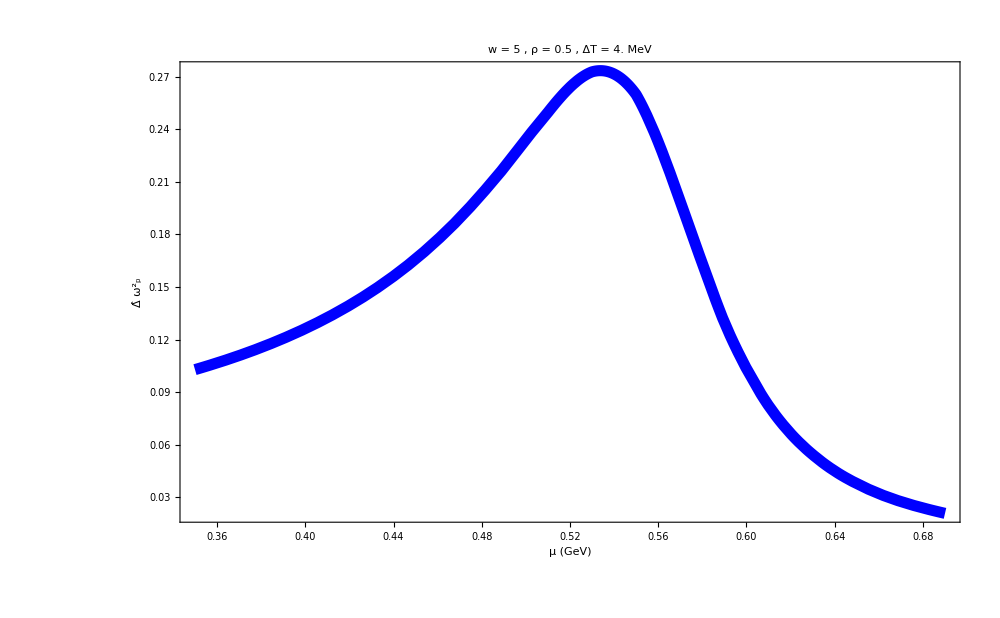

```mathematica
Np2Plot2=Plot[{Interpolation[Table[{Tab1[[i,1]],Tab1[[i,2]]},{i,1,Length[Tab1]}]][x]},{x,Min[Ulist],Max[Ulist]},PlotRange->All,Frame->True,FrameLabel->{"μ (GeV)","Δ̂ (ω^2)_p "}, LabelStyle->{42,Bold,Black},PlotLabel->StringJoin["w = ",ToString[w]," , ρ = ",ToString[ρ], " , ΔT = ",ToString[DelT1*1000]," MeV"],PlotStyle->{{Blue,Thickness[0.008]}},ImageSize->1000]
```

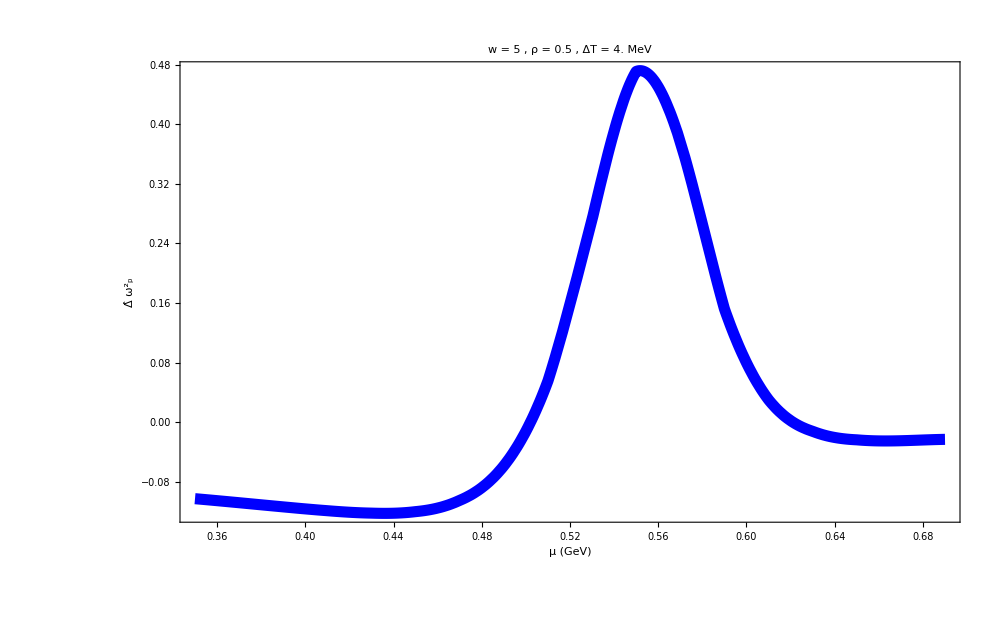

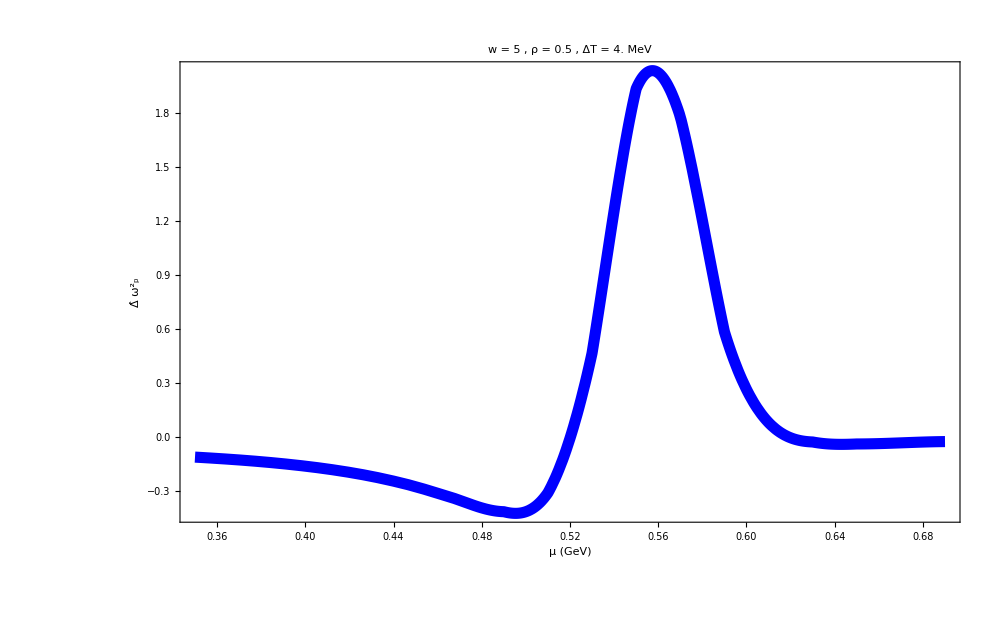

```mathematica
Np3Plot2=Plot[{Interpolation[Table[{Tab1[[i,1]],Tab1[[i,3]]},{i,1,Length[Tab1]}]][x]},{x,Min[Ulist],Max[Ulist]},PlotRange->All,Frame->True,FrameLabel->{"μ (GeV)","Δ̂ (ω^2)_p "}, LabelStyle->{42,Bold,Black},PlotLabel->StringJoin["w = ",ToString[w]," , ρ = ",ToString[ρ], " , ΔT = ",ToString[DelT1*1000]," MeV"],PlotStyle->{{Blue,Thickness[0.008]}},ImageSize->1000]
Np4Plot2=Plot[{Interpolation[Table[{Tab1[[i,1]],Tab1[[i,4]]},{i,1,Length[Tab1]}]][x]},{x,Min[Ulist],Max[Ulist]},PlotRange->All,Frame->True,FrameLabel->{"μ (GeV)","Δ̂ (ω^2)_p "}, LabelStyle->{42,Bold,Black},PlotLabel->StringJoin["w = ",ToString[w]," , ρ = ",ToString[ρ], " , ΔT = ",ToString[DelT1*1000]," MeV"],PlotStyle->{{Blue,Thickness[0.008]}},ImageSize->1000]
```